```mathematica
ClearAll["Global`*"];
NotebookFind[EvaluationNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookFind[EvaluationNotebook[],"Print",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookDelete@Cells@MessagesNotebook[];
On[Assert];
```

```mathematica
Get[NotebookDirectory[]<>"VecG.m"]
Get[NotebookDirectory[]<>"Functions.m"];

G=SymmetricGroup[3];(*Left fusion category*)
H=PermutationGroup[{Cycles[{{1,2}}]}];(*Subgp of G labelling the module*)

(*G=DihedralGroup[4];(*Left fusion category*)
H=PermutationGroup[{Cycles[{{1,3},{2,4}}]}];(*Subgp of G labelling the module*)*)
```

```mathematica
computeMoritaDual[G,H];(*Computes all data as discussed in paper*)
```

Computing module action

Computing irreps

Computing intertwiners

Verifying isometric

Isometric: ✓

```mathematica
fusionTable["C"](*Fusion rules for left fusion category (input data)*)
fusionTable["L"](*Fusion rules for M as left module category (input data)*)
fusionTable["R"](*Fusion rules for M as right module category (computed)*)
fusionTable["D"](*Fusion rules for right fusion category (computed)*)
dim[#]&/@obsD
```

| 1 | σ_2\[PermutationProduct]σ_1 | σ_1 | σ_2 | σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2
1 | 1 | σ_2\[PermutationProduct]σ_1 | σ_1 | σ_2 | σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2
σ_2\[PermutationProduct]σ_1 | σ_2\[PermutationProduct]σ_1 | 1 | σ_2 | σ_1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2^2
σ_1 | σ_1 | σ_2^2 | 1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1 | σ_2
σ_2 | σ_2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1 | σ_2^2 | 1 | σ_1
σ_2^2 | σ_2^2 | σ_1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | 1 | σ_2 | σ_2\[PermutationProduct]σ_1
σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2 | σ_2^2 | σ_2\[PermutationProduct]σ_1 | σ_1 | 1

| H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
1 | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_1 | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H
σ_2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | H
σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | H

| ℼ_0 | ℼ_1 | ℼ_2
H | H | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H⊕σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | H⊕σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | H⊕σ_2\[PermutationProduct]σ_1\[PermutationProduct]H

| ℼ_0 | ℼ_1 | ℼ_2
ℼ_0 | ℼ_0 | ℼ_1 | ℼ_2
ℼ_1 | ℼ_1 | ℼ_0 | ℼ_2
ℼ_2 | ℼ_2 | ℼ_2 | ℼ_0⊕ℼ_1⊕ℼ_2

{1,1,2}

```mathematica
Fs[0](*F-symbols for left fusion category (input data)*)
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Fs[1](*F-symbols for M as a left module category (input data)*)
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Fs[2](*F-symbols for M as a bimodule category (computed using Eq.13)*)
```

{1,1,1,1,1,1,1,1,1,1,1,1,Root-0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,1]-0.6047795766403344,Root0.291+0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,4]0.29141369364462055,Root0.201-0.980 ⅈRoot[64105+117806 #1^2+64105 #1^4&,3]0.20143003297867212,Root0.212-0.977 ⅈRoot[574643225+1046385714 #1^2+574643225 #1^4&,3]0.21158267302939068,Root-0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,2]-0.6047795766403344,Root0.291-0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,3]0.29141369364462055,Root0.201+0.980 ⅈRoot[64105+117806 #1^2+64105 #1^4&,4]0.20143003297867212,Root0.212+0.977 ⅈRoot[574643225+1046385714 #1^2+574643225 #1^4&,4]0.21158267302939068,1,-1,Root0.775+0.632 ⅈRoot[29377764245-11802705894 #1^2+29377764245 #1^4&,4]0.7748800612244531,Root0.775-0.632 ⅈRoot[29377764245-11802705894 #1^2+29377764245 #1^4&,3]0.7748800612244531,1,-1,Root0.945+0.328 ⅈRoot[17225-27054 #1^2+17225 #1^4&,4]0.9448047540217296,Root0.945-0.328 ⅈRoot[17225-27054 #1^2+17225 #1^4&,3]0.9448047540217296,Root0.837+0.547 ⅈRoot[6749895965-5415722072 #1^2+6749895965 #1^4&,4]0.8370097911636798,Root0.960-0.279 ⅈRoot[2669034289-4505746078 #1^2+2669034289 #1^4&,3]0.9602286102621652,Root-0.969-0.248 ⅈRoot[13656224045-23964437046 #1^2+13656224045 #1^4&,1]-0.9688699930761064,Root-0.831-0.557 ⅈRoot[4600648705-3500443394 #1^2+4600648705 #1^4&,1]-0.8307915889047264,Root0.837-0.547 ⅈRoot[6749895965-5415722072 #1^2+6749895965 #1^4&,3]0.8370097911636798,Root0.960+0.279 ⅈRoot[2669034289-4505746078 #1^2+2669034289 #1^4&,4]0.9602286102621652,Root-0.969+0.248 ⅈRoot[13656224045-23964437046 #1^2+13656224045 #1^4&,2]-0.9688699930761064,Root-0.831+0.557 ⅈRoot[4600648705-3500443394 #1^2+4600648705 #1^4&,2]-0.8307915889047264,Root-0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,1]-0.6047795766403344,Root-0.291-0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,1]-0.29141369364462055,Root0.520-0.854 ⅈRoot[33361+30622 #1^2+33361 #1^4&,3]0.5201206243411157,Root-0.131-0.991 ⅈRoot[44168345+85322994 #1^2+44168345 #1^4&,1]-0.13060631071833564,Root0.837+0.547 ⅈRoot[6749895965-5415722072 #1^2+6749895965 #1^4&,4]0.8370097911636798,Root-0.960+0.279 ⅈRoot[2669034289-4505746078 #1^2+2669034289 #1^4&,2]-0.9602286102621652,Root-0.594-0.804 ⅈRoot[353616001+207709502 #1^2+353616001 #1^4&,1]-0.5942669497511468,Root-0.996+0.0939 ⅈRoot[7106860469-13963258662 #1^2+7106860469 #1^4&,2]-0.995584963282931,Root-0.0704+0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,2]-0.07042985588673913,Root0.547-0.837 ⅈRoot[107117+86070 #1^2+107117 #1^4&,3]0.5469200319307631,Root-0.438-0.899 ⅈRoot[213029+262842 #1^2+213029 #1^4&,1]-0.4376551115085563,Root-0.720-0.694 ⅈRoot[95016545-6863934 #1^2+95016545 #1^4&,1]-0.7197637382829146,Root-0.0704-0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,1]-0.07042985588673913,Root0.547+0.837 ⅈRoot[107117+86070 #1^2+107117 #1^4&,4]0.5469200319307631,Root-0.438+0.899 ⅈRoot[213029+262842 #1^2+213029 #1^4&,2]-0.4376551115085563,Root-0.720+0.694 ⅈRoot[95016545-6863934 #1^2+95016545 #1^4&,2]-0.7197637382829146,Root-0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,2]-0.6047795766403344,Root-0.291+0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,2]-0.29141369364462055,Root-0.131+0.991 ⅈRoot[44168345+85322994 #1^2+44168345 #1^4&,2]-0.13060631071833564,Root0.520+0.854 ⅈRoot[33361+30622 #1^2+33361 #1^4&,4]0.5201206243411157,Root0.837-0.547 ⅈRoot[6749895965-5415722072 #1^2+6749895965 #1^4&,3]0.8370097911636798,Root-0.960-0.279 ⅈRoot[2669034289-4505746078 #1^2+2669034289 #1^4&,1]-0.9602286102621652,Root-0.996-0.0939 ⅈRoot[7106860469-13963258662 #1^2+7106860469 #1^4&,1]-0.995584963282931,Root-0.594+0.804 ⅈRoot[353616001+207709502 #1^2+353616001 #1^4&,2]-0.5942669497511468,Root-0.0704-0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,1]-0.07042985588673913,Root-0.547-0.837 ⅈRoot[107117+86070 #1^2+107117 #1^4&,1]-0.5469200319307631,Root-0.907+0.420 ⅈRoot[137905-178466 #1^2+137905 #1^4&,2]-0.9074859180273847,Root-0.119+0.993 ⅈRoot[3669424525+7131316214 #1^2+3669424525 #1^4&,2]-0.1189089201417809,1,-1,Root0.941+0.337 ⅈRoot[2138606905-3303274546 #1^2+2138606905 #1^4&,4]0.9413543080566384,Root0.941-0.337 ⅈRoot[2138606905-3303274546 #1^2+2138606905 #1^4&,3]0.9413543080566384,Root-0.0704+0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,2]-0.07042985588673913,Root-0.547+0.837 ⅈRoot[107117+86070 #1^2+107117 #1^4&,2]-0.5469200319307631,Root-0.119-0.993 ⅈRoot[3669424525+7131316214 #1^2+3669424525 #1^4&,1]-0.1189089201417809,Root-0.907-0.420 ⅈRoot[137905-178466 #1^2+137905 #1^4&,1]-0.9074859180273847}

```mathematica
Fs[3](*F-symbols for M as a right module category (computed using intertwiners)*)
```

{1,-1,1,1,-1,-1,1,-1,-1,Root-0.837-0.547 ⅈRoot[6749895965-5415722072 #1^2+6749895965 #1^4&,1]-0.8370097911636798,1,Root0.960-0.279 ⅈRoot[2669034289-4505746078 #1^2+2669034289 #1^4&,3]0.9602286102621652,Root-0.663+0.246 ⅈRoot[480041358365482424214949128481+79713655323445317777071901432 #1^2-808468300174930812486994719976 #1^4+318854621293781271108287605728 #1^6+7680661733847718787439186055696 #1^8&,2]-0.6628545480748294,Root0.686-0.173 ⅈRoot[1638896627671800528844020044161-5333088196036606305831712716808 #1^2+11571896950814730844915576427544 #1^4-21332352784146425223326850867232 #1^6+26222346042748808461504320706576 #1^8&,7]0.6856033711386137,Root-0.308+0.951 ⅈRoot[1365015346178940625+2212573034603172446 #1^2+1365015346178940625 #1^4&,2]-0.3078496375038097,Root0.689+0.160 ⅈRoot[71012035261166039085051646225-323093499448871768211871611720 #1^2+812757591452911567205449795736 #1^4-1292373997795487072847486446880 #1^6+1136192564178656625360826339600 #1^8&,8]0.6887571590765666,Root0.667+0.234 ⅈRoot[40972415691795013221100501104025+26609664320093312185383886604920 #1^2-155982280763076203473168812937896 #1^4+106438657280373248741535546419680 #1^6+655558651068720211537608017664400 #1^8&,8]0.6673977360888792,1,Root-0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,1]-0.6047795766403344,Root0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,4]0.6047795766403344,Root-0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,1]-0.6047795766403344,Root-0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,1]-0.6047795766403344,Root0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,4]0.6047795766403344,Root-0.0580+0.998 ⅈRoot[8657849317105+17199006795408 #1^2+8657849317105 #1^4&,2]-0.05804772913712978,Root0.291+0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,4]0.29141369364462055,Root-0.291-0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,1]-0.29141369364462055,Root0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,3]0.6047795766403344,Root-0.837-0.547 ⅈRoot[6749895965-5415722072 #1^2+6749895965 #1^4&,1]-0.8370097911636798,Root0.291-0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,3]0.29141369364462055,Root-0.960+0.279 ⅈRoot[2669034289-4505746078 #1^2+2669034289 #1^4&,2]-0.9602286102621652,Root0.205-0.677 ⅈRoot[93350294672860767797172257745528915025+446940273087965403969655180856835767040 #1^2+1200144379957705750522587929306234688136 #1^4+1787761092351861615878620723427343068160 #1^6+1493604714765772284754756123928462640400 #1^8&,5]0.20479374326424749,Root0.0343-0.706 ⅈRoot[1017520261648905389366653050871441075129+1561506430908434980336965320761229809800 #1^2-1771017603809021192554861149288919463848 #1^4+6246025723633739921347861283044919239200 #1^6+16280324186382486229866448813943057202064 #1^8&,5]0.03425033828297142,Root-0.996-0.0892 ⅈRoot[11796983409361-23218148777122 #1^2+11796983409361 #1^4&,1]-0.9960098982141865,Root-0.144+0.692 ⅈRoot[79033975885918706019849662981371431159450810295865292025+351198623523762245660117910333314975684427871785997607040 #1^2+856631008739970137179084601242116639661058102578302707656 #1^4+1404794494095048982640471641333259902737711487143990428160 #1^6+1264543614174699296317594607701942898551212964733844672400 #1^8&,4]-0.14357696364826708,Root-0.0289-0.707 ⅈRoot[861472072524404912050454750694088499135374528143433868449+1844882430339106718529999539855272897570029748741863397320 #1^2+555119278050547040946408763181732083515740624716093234712 #1^4+7379529721356426874119998159421091590280118994967453589280 #1^6+13783553160390478592807276011105415986165992450294941895184 #1^8&,3]-0.028916464016357828,Root0.781-0.624 ⅈRoot[1082203506083184199463125-478687155620268877893146 #1^2+1082203506083184199463125 #1^4&,3]0.7813972063919137,Root-0.0704-0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,1]-0.07042985588673913,Root0.0704+0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,4]0.07042985588673913,Root-0.0704-0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,1]-0.07042985588673913,Root-0.0704-0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,1]-0.07042985588673913,Root0.0704+0.998 ⅈRoot[484037+958470 #1^2+484037 #1^4&,4]0.07042985588673913,Root0.885+0.465 ⅈRoot[5553865557388493-6298919430181770 #1^2+5553865557388493 #1^4&,4]0.885176607469146,Root0.547+0.837 ⅈRoot[107117+86070 #1^2+107117 #1^4&,4]0.5469200319307631,Root-0.547-0.837 ⅈRoot[107117+86070 #1^2+107117 #1^4&,1]-0.5469200319307631,Root0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,3]0.6047795766403344,-1,Root-0.291+0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,2]-0.29141369364462055,-1,Root-0.208+0.676 ⅈRoot[16637538796410101847300036155280498282025+79901997464294127176461934804399116403640 #1^2+215391476346346453307294506333906638258136 #1^4+319607989857176508705847739217596465614560 #1^6+266200620742561629556800578484487972512400 #1^8&,4]-0.20815405843781098,Root-0.561+0.431 ⅈRoot[1626711472217476383707077976233164069025-6106023095626709682321663818213068337160 #1^2+17572579888822341130178521399184446798616 #1^4-24424092382506838729286655272852273348640 #1^6+26027383555479622139313247619730625104400 #1^8&,4]-0.5605998238565046,Root-0.834+0.552 ⅈRoot[69784341459610838125-54572977057608565066 #1^2+69784341459610838125 #1^4&,2]-0.833969910061988,Root0.259+0.658 ⅈRoot[95221257841739402385535338288950690746295884084791624808609-33827551698240235278861003988303045710702571687695017755080 #1^2-154403675002297634492942409032030135166257021773762389842408 #1^4-135310206792960941115444015953212182842810286750780071020320 #1^6+1523540125467830438168565412623211051940734145356665996937744 #1^8&,6]0.2586848989982738,Root0.170-0.686 ⅈRoot[55089478065015899317144078327786532364402289617570830641+4398473924325626472379553192623890362589128713215908280 #1^2-234187954789792194486971275060888295823864032230625266792 #1^4+17593895697302505889518212770495561450356514852863633120 #1^6+881431649040254389074305253244584517830436633881133290256 #1^8&,5]0.1695032470611128,Root-0.834+0.551 ⅈRoot[9409138367005-7377674033194 #1^2+9409138367005 #1^4&,2]-0.8342806283005342}

```mathematica
Fs[4](*F-symbols for right fusion category (computed as maps between intertwiners)*)
```

{1,-1,1,1,-1,-1,1,1,1,-1,1,-1,1,-1,-1,1,-1,1,1,Root0.994-0.108 ⅈRoot[222162378294989678769520812087590641-191017715996031887674201676437361604 #1^2-30109036723953396768756402986243674 #1^4-191017715996031887674201676437361604 #1^6+222162378294989678769520812087590641 #1^8&,7]0.9941294980904457,Root0.994+0.108 ⅈRoot[222162378294989678769520812087590641-191017715996031887674201676437361604 #1^2-30109036723953396768756402986243674 #1^4-191017715996031887674201676437361604 #1^6+222162378294989678769520812087590641 #1^8&,8]0.9941294980904457,-1,Root0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,4]0.6047795766403344,Root-0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,1]-0.6047795766403344,Root0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,4]0.6047795766403344,Root0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,4]0.6047795766403344,Root0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,4]0.6047795766403344,Root-0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,1]-0.6047795766403344,Root0.0580-0.998 ⅈRoot[8657849317105+17199006795408 #1^2+8657849317105 #1^4&,3]0.05804772913712978,Root0.291+0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,4]0.29141369364462055,Root0.291+0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,4]0.29141369364462055,Root-0.291-0.957 ⅈRoot[24917+41370 #1^2+24917 #1^4&,1]-0.29141369364462055,Root0.605-0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,3]0.6047795766403344,Root-0.605+0.796 ⅈRoot[13945+7488 #1^2+13945 #1^4&,2]-0.6047795766403344,1,Root0.393-0.919 ⅈRoot[137931043041068416247954039413455120876775849+194150185817716396335846707468057252983755780 #1^2+280821472140124579316915031558946466409211318 #1^4+194150185817716396335846707468057252983755780 #1^6+137931043041068416247954039413455120876775849 #1^8&,5]0.39320366804014645,Root0.186-0.983 ⅈRoot[137931043041068416247954039413455120876775849+2753987509586848838170593348884253039973380 #1^2-196873039992123434337035226800710002455812682 #1^4+2753987509586848838170593348884253039973380 #1^6+137931043041068416247954039413455120876775849 #1^8&,5]0.18620222995907254,-1,Root0.302-0.398 ⅈRoot[13945+29952 #1^2+223120 #1^4&,3]0.3023897883201672,Root-0.197+0.460 ⅈRoot[137931043041068416247954039413455120876775849+776600743270865585343386829872229011935023120 #1^2+4493143554241993269070640504943143462547381088 #1^4+12425611892333849365494189277955664190960369920 #1^6+35310347018513514559476234089844510944454617344 #1^8&,4]-0.19660183402007322,Root-0.486+0.514 ⅈRoot[7620271968513962297166276412588345727804932406054775390625-28422009445049381418027851396580217977641797283329550325000 #1^2+54357412838851904372526070355129408611639235860363694327576 #1^4-113688037780197525672111405586320871910567189133318201300000 #1^6+121924351496223396754660422601413531644878918496876406250000 #1^8&,4]-0.4860897514970162,Root-0.258+0.429 ⅈRoot[43202368124438035277299294919009441010549025-167262269234468126641585847205987103620318720 #1^2+145066149296416434987766668604137296347538464 #1^4-2676196307751490026265373555295793657925099520 #1^6+11059806239856137030988619499266416898700550400 #1^8&,4]-0.2575310383721683,Root0.146-0.478 ⅈRoot[24917+165480 #1^2+398672 #1^4&,3]0.14570684682231028,Root-0.428+0.563 ⅈRoot[4396732886618582763149758431149350237633128093385042978515625+16550689943895196818004131576934020430289216428336042751075000 #1^2+47874410546554660966715406234156442788619796950481959714299864 #1^4+66202759775580787272016526307736081721156865713344171004300000 #1^6+70347726185897324210396134898389603802130049494160687656250000 #1^8&,2]-0.4276734844144381,Root-0.703+0.0765 ⅈRoot[1481861138319929863042903039178077789974773765601939938156494140625-3310707015435429791004949095140099184559899481145110797343398000000 #1^2+2175876090379830544948034875161378913277477635444384655044686571144 #1^4-13242828061741719164019796380560396738239597924580443189373592000000 #1^6+23709778213118877808686448626849244639596380249631039010503906250000 #1^8&,2]-0.7029516673513612,Root-0.663+0.245 ⅈRoot[2729741901750003023918182860664906282908314631397539262772504775390625-9890313353717834365051634926664686004908484885771936231901433624275000 #1^2+26680649954533451543996179288858275648464170375833405901041655780021784 #1^4-39561253414871337460206539706658744019633939543087744927605734497100000 #1^6+43675870428000048382690925770638500526533034102360628204360076406250000 #1^8&,2]-0.663301455994982,1,-1,0}

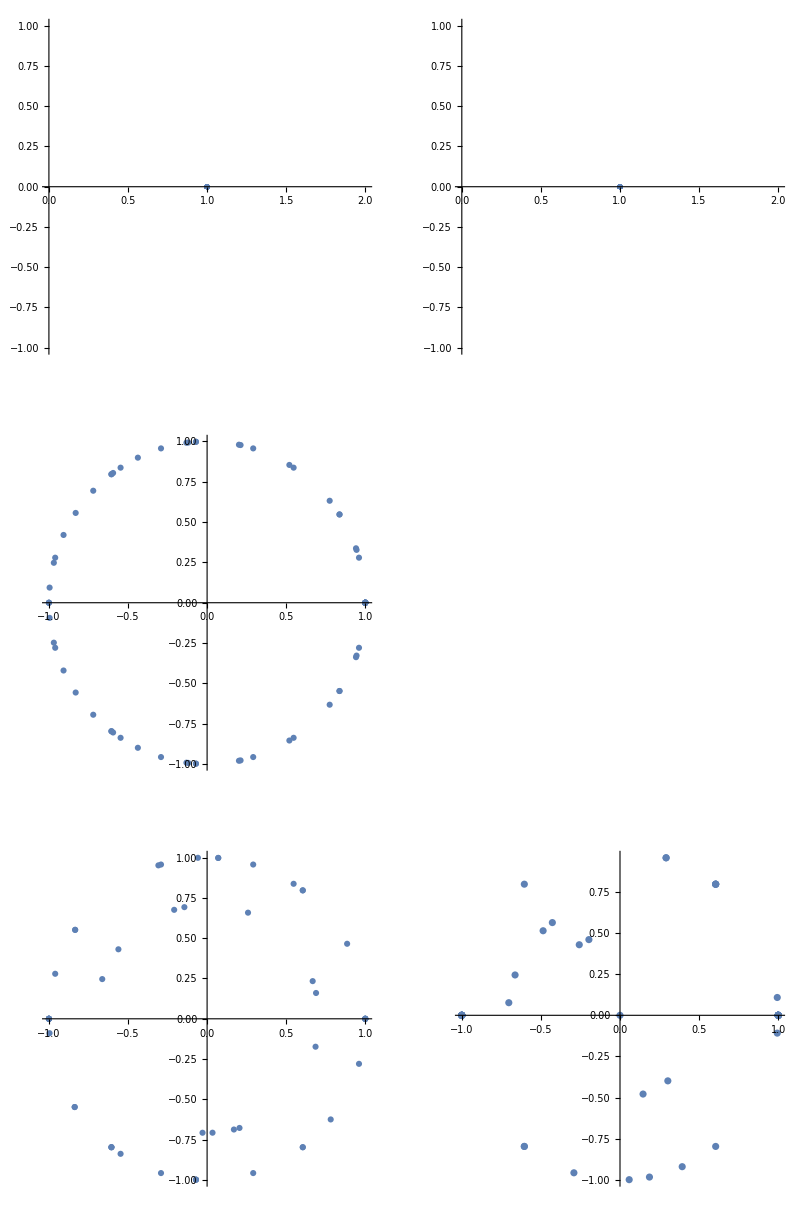

```mathematica
plt[n_]:=ListPlot[{Re[#],Im[#]}&/@Fs[n],AspectRatio->1]
GraphicsGrid[{{plt[0],plt[1]},{plt[2]},{plt[3],plt[4]}}]
```

```mathematica
verifyData[](*Check data is unitary and obeys pentagons*)
```

Pentagons: ✓

Unitary: ✓

```mathematica
verifyInvertibility[](*Verify invertiblility formula holds*)
```

Invertibility criteria: ✓

```mathematica
schurOrthogQ[](*Verify matrix element orthogonalityholds*)
```

Schur orthogonality: ✓